# DM DM -> h2 h2

```mathematica
Quit;
```

```mathematica
ClearAll["Global`*"];
$FeynArtsPath=SetDirectory["~/Work/FeynArts-3.9"]
<<FeynArts`
SetDirectory[$FeynArtsPath<>""]
$FormCalcPath=SetDirectory["~/Work/FormCalc-8.3"]
<<FormCalc`
SetDirectory[$FormCalcPath<>""]
```

/home/anferivera/Work/FeynArts-3.9

FeynArts 3.9 (8 Jul 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

/home/anferivera/Work/FeynArts-3.9

/home/anferivera/Work/FormCalc-8.3

FormCalc 8.3

by Thomas Hahn

last revised 14 Nov 13

/home/anferivera/Work/FormCalc-8.3

## Load the model, choose the topology and the diagram

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

loading generic model file /home/anferivera/Work/FeynArts-3.9/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/anferivera/Work/FeynArts-3.9/Models/SDdiracDMEWSB.mod

> 54 particles (incl. antiparticles) in 19 classes

> $CounterTerms are ON

> 112 vertices

classes model {SDdiracDMEWSB} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

in total: 6 Particles insertions

> Top. 1: 2 diagrams

> Top. 2: 2 diagrams

> Top. 3: 2 diagrams

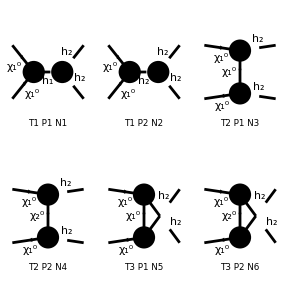

FeynArtsGraphics[{ComposedChar[\chi,1,0],ComposedChar[\chi,1,0]}→{ComposedChar[h,2],ComposedChar[h,2]}][([T1 P1 N1] | [T1 P2 N2] | [T2 P1 N3]
[T2 P2 N4] | [T3 P1 N5] | [T3 P2 N6])]

```mathematica
ClearProcess[];
n22=CreateTopologies[0,2->2]

d22=InsertFields[n22,{F[6,{1}],-F[6,{1}]}->{S[1,{2}],S[1,{2}]}, InsertionLevel->{Particles},Model->"SDdiracDMEWSB",GenericModel->"Lorentz"(*,ExcludeParticles->{S[1,{1}],F[6,{2}] }*) ];
Paint[d22,ColumnsXRows->{3,2}]
```

## Amplitude

```mathematica
amp=CreateFeynAmp[d22];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

in total: 6 Particles amplitudes

```mathematica
resultamp = CalcFeynAmp[amp,FermionChains->VA,FermionOrder->None,  Invariants->True];
```

preparing FORM code in /home/anferivera/Work/FormCalc-8.3/fc-amp-1.frm

running FORM...

ok

#### Rotation matrices in the Fermion Singlet limit (YD->0 -> No mixing)

```mathematica
Den[x_,y_]:=1/(x-y)
expr0=Simplify[Simplify[ComplexExpand[Plus@@resultamp//.Subexpr[]//.Abbr[]]/.Alfa->e^2/(4Pi)/.{MassFxv[1]->mx1,MassFxv[2]->mx2,Masshh[1]->mh1,Masshh[2]->mh2}/.{ZH[1,1]->Z11,ZH[1,2]->Z12,ZH[2,1]->-Z12,ZH[2,2]->Z11}/.{XV[1,1]->0,XV[1,2]->1,XV[2,1]->-1,XV[2,2]->0}/.{XU[1,1]->0,XU[1,2]->1,XU[2,1]->-1,XU[2,2]->0}/.YRD->0]/.(Z11^2+Z12^2)->1]
```

1/2 YRC ((2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2-(√2 (3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (S (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-S) (-mh1^2+S))) Mat[<v2|1|u1>]-((T-U) YRC Z11^2 Mat[<v2|1,k[3]|u1>])/((mx1^2-T) (mx1^2-U)))

#### Kind of Dirac Chains in the AMPLITUDE

```mathematica
InputForm[expr0/.{Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]->0,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]->0,
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]->0,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]->0}]
```

0

```mathematica
expr2 = Simplify[expr0/.{Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]->F1,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]->F5,
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]->F13,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]->F53}]
```

1/2 YRC (-(F13 (T-U) YRC Z11^2)/((mx1^2-T) (mx1^2-U))+F1 (2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2-(√2 (3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (S (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-S) (-mh1^2+S))))

#### Factors in the AMPLITUDE

```mathematica
M1=Simplify[D[expr2,F1]]
```

1/2 YRC (2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2-(√2 (3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (S (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-S) (-mh1^2+S)))

```mathematica
M2=Simplify[D[expr2,F5]]
```

0

```mathematica
M3=Simplify[D[expr2,F13]]
```

-((T-U) YRC^2 Z11^2)/(2 (mx1^2-T) (mx1^2-U))

```mathematica
M4=Simplify[D[expr2,F53]]
```

0

#### Factorization of the Amplitude

```mathematica
expr3 =(M1*F1+M2*F5+M3*F13+M4*F53);
```

```mathematica
Simplify[expr2 -expr3]
```

0

## Momenta in the computation for the CM frame

```mathematica
kinematic=Solve[{E1==Sqrt[p1^2+mx1^2]&&E2==Sqrt[p2^2+mh2^2]&& E2==E1},{E1,E2,p2}][[1]]
```

{E1→√(mx1^2+p1^2),E2→√(mx1^2+p1^2),p2→-√(-mh2^2+mx1^2+p1^2)}

In two dimensions...

```mathematica
k1={E1,p1,0,0};
k2={E1,-p1,0,0};
k3={E2,p2*ct,p2*st,0}/.st->Sqrt[1-ct^2];
k4={E2,-p2*ct,-p2*st,0}/.st->Sqrt[1-ct^2];
```

#### Mandelstan variables

```mathematica
guv = {{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}};
MatrixForm[guv]
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
MV = Simplify[{S->(k1 + k2).guv.(k1 + k2),   
		         T->(k1 - k3).guv.(k1 - k3),   
                            U ->(k1 - k4).guv.(k1 - k4)}/.kinematic]
```

{S→4 (mx1^2+p1^2),T→mh2^2-mx1^2-2 p1 (p1+ct √(-mh2^2+mx1^2+p1^2)),U→mh2^2-mx1^2-2 p1 (p1-ct √(-mh2^2+mx1^2+p1^2))}

## Dirac spinors and Gamma matrices

Dirac matrices

```mathematica
gamma0={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
gamma1={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
gamma2={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
gamma3={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};

gamma5={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};
gammamu={gamma0,gamma1,gamma2,gamma3};
```

```mathematica
Grid[{{"γ0","γ1","γ2","γ3","γ5"},{gamma0//MatrixForm,gamma1//MatrixForm,gamma2//MatrixForm,gamma3//MatrixForm,gamma5//MatrixForm}},Frame->All]
```

γ0 | γ1 | γ2 | γ3 | γ5
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1) | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

Check properties of gamma matrices ...

[γu,γv]=2guv

```mathematica
Grid[{{"i=0","i=1","i=2","i=3"},{ Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma0}},{j,{gamma0}}]]//MatrixForm,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma1}},{j,{gamma1}}]]//MatrixForm,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma2}},{j,{gamma2}}]] //MatrixForm ,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma3}},{j,{gamma3}}]]//MatrixForm} },Frame->All]
```

i=0 | i=1 | i=2 | i=3
(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2)

```mathematica
χ[s_]:=If[s==1,{1,0},{0,1}]
Grid[{{χ1,χ2},{χ[1]//MatrixForm,χ[-1]//MatrixForm}},Frame->All]
```

χ1 | χ2
(1
0) | (0
1)

Spinors (Cheng appendix)

```mathematica
σp1=((Total[k1[[#+1]] PauliMatrix[#]&/@Range[3]])/(k1[[1]]+mx1));
σp2=((Total[k2[[#+1]] PauliMatrix[#]&/@Range[3]])/(k2[[1]]+mx1));
σp3=((Total[k3[[#+1]] PauliMatrix[#]&/@Range[3]])/(k3[[1]]+mx1));
σp4=((Total[k4[[#+1]] PauliMatrix[#]&/@Range[3]])/(k4[[1]]+mx1));
```

```mathematica
uspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{χ[s],Dot[eif,χ[s]]},1]
uspinor[1,σp2,mx1,k2[[1]]]
```

{√(E1+mx1),0,0,-p1/(√(E1+mx1))}

```mathematica
vspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{Dot[eif,χ[s]],χ[s]},1]
vspinor[1,σp2,mx1,k2[[1]]]
```

{0,-p1/(√(E1+mx1)),√(E1+mx1),0}

Check normalization for the U Spinors (input and output)

```mathematica
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp1,mx1,k1[[1]]]]).gamma0.uspinor[1,σp1,mx1,k1[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}]
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp2,mx1,k2[[1]]]]).gamma0.uspinor[1,σp2,mx1,k2[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}];
Simplify[Simplify[(Conjugate[uspinor[1,σp3,mx1,k3[[1]]]]).gamma0.uspinor[1,σp3,mx1,k3[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{p1^2-> E1^2-mx1^2,st->Sqrt[1-ct^2]}];
Simplify[Simplify[(Conjugate[uspinor[1,σp4,mx1,k4[[1]]]]).gamma0.uspinor[1,σp4,mx1,k4[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{(ct^2+st^2)->1,p1^2-> E1^2-mx1^2}];
```

2 mx1

Check normalization for the V Spinors

```mathematica
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp1,mx1,k1[[1]]]]).gamma0.vspinor[1,σp1,mx1,k1[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}]
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp2,Me,k2[[1]]]]).gamma0.vspinor[1,σp2,mx1,k2[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}];
Simplify[Simplify[(Conjugate[vspinor[1,σp3,mx1,k3[[1]]]]).gamma0.vspinor[1,σp3,mx1,k3[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{p1^2-> E1^2-mx1^2,st->Sqrt[1-ct^2]}];
Simplify[Simplify[(Conjugate[vspinor[1,σp4,mx1,k4[[1]]]]).gamma0.vspinor[1,σp4,mx1,k4[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{(ct^2+st^2)->1,p1^2-> E1^2-mx1^2}];
```

-2 mx1

(OverBar[U1]γaU2)^†=(OverBar[U2]γaU1)

```mathematica
AA1=(Conjugate[uspinor[1,σp1,mx1,k1[[1]]]]).gamma0.gamma2.uspinor[1,σp3,mx1,k3[[1]]];
AA2=(Conjugate[uspinor[1,σp3,mx1,k3[[1]]]]).gamma0.gamma2.uspinor[1,σp1,mx1,k1[[1]]];
Simplify[Conjugate[AA1]-AA2]
```

0

```mathematica
BB1=Simplify[(Conjugate[vspinor[1,σp1,mx1,k1[[1]]]]).gamma0.gamma2.vspinor[1,σp4,mx1,k3[[1]]]/.E2->E1,Element[{√(E1+mx1),1/(√(E1+mx1)),p1,p2,st,ct},Reals]];
BB2=Simplify[(Conjugate[vspinor[1,σp4,mx1,k3[[1]]]]).gamma0.gamma2.vspinor[1,σp1,mx1,k1[[1]]]/.E2->E1,Element[{√(E1+mx1),1/(√(E1+mx1)),p1,p2,st,ct},Reals]];
Simplify[Simplify[(Conjugate[BB1]-BB2),Element[{√(E1+mx1),1/(√(E1+mx1)),p1,p2,st,ct},Reals]]]
```

0

## Amplitude square

Manipulation of the amplitude

#### Dirac Chains in the amplitude (F1,F5,F13,F53)

```mathematica
Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]
```

Mat[<v2|1|u1>]

Mat[<v2|5|u1>]

Mat[<v2|1,k[3]|u1>]

Mat[<v2|5,k[3]|u1>]

#### FULL Amplitude

```mathematica
AMP[s1_,s2_]:=expr3/.{
F1->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,IdentityMatrix[4]],uspinor[s1,σp1,mx1,k1[[1]]]],
F5->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,gamma5],uspinor[s1,σp1,mx1,k1[[1]]]],
F13->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,(k3[[1]]*gamma0-k3[[2]]*gamma1-k3[[3]]*gamma2-k3[[4]]*gamma3)],uspinor[s1,σp1,mx1,k1[[1]]]],
F53->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,gamma5,(k3[[1]]*gamma0-k3[[2]]*gamma1-k3[[3]]*gamma2-k3[[4]]*gamma3)],uspinor[s1,σp1,mx1,k1[[1]]]]
}
```

```mathematica
AMP[1,-1]
```

1/2 YRC (2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2-(√2 (3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (S (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-S) (-mh1^2+S))) (-(p1 (√(E1+mx1))^*)/(√(E1+mx1))-√(E1+mx1) (1/(√(E1+mx1)))^* p1^*)-((T-U) YRC^2 Z11^2 (√(E1+mx1) ((-ct p2-ⅈ √(1-ct^2) p2) (√(E1+mx1))^*-E2 (1/(√(E1+mx1)))^* p1^*)+(p1 (E2 (√(E1+mx1))^*-(-ct p2+ⅈ √(1-ct^2) p2) (1/(√(E1+mx1)))^* p1^*))/(√(E1+mx1))))/(2 (mx1^2-T) (mx1^2-U))

Sum over spinors and gamma matrices.. trick! Warning: I do the gamma matrices explicitly because i need to avoid the index in the gamma_uv.

#### FULL Amplitude squared

```mathematica
AMP2=Simplify[(1/4)*(Sum[AMP[s1,s2]*Conjugate[AMP[s1,s2]],{s1,{-1,1}},{s2,{-1,1}}]/.{√(1-ct^2)->st})/.{Conjugate[mx1]->mx1,Conjugate[mx2]->mx2,Conjugate[mh1]->mh1,Conjugate[mh2]->mh2,Conjugate[√(E1+mx1)]->√(E1+mx1),Conjugate[1/(√(E1+mx1))]->1/(√(E1+mx1)),Conjugate[E1]->E1,Conjugate[E2]->E2,Conjugate[p1]->p1,Conjugate[p2]->p2,Conjugate[st]->st,Conjugate[ct]->ct,Conjugate[Lam]->Lam,Conjugate[Z11]->Z11,Conjugate[Z12]->Z12,Conjugate[Z21]->Z21,Conjugate[Z22]->Z22,Conjugate[vvSM]->vvSM,Conjugate[LSP]->LSP,Conjugate[LSPH]->LSPH}/.{st->Sqrt[1-ct^2],Z22->Z11,Z21->-Z12}]
```

1/8 YRC^2 (((ct (E1^2+2 E1 mx1+mx1^2-p1^2)-ⅈ √(1-ct^2) (E1^2+2 E1 mx1+mx1^2+p1^2)) p2 (T-U) YRC Z11^2)/((E1+mx1) (mx1^2-T) (mx1^2-U))-2 p1 (2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2-(√2 (3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (S (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-S) (-mh1^2+S)))) (((ct (E1^2+2 E1 mx1+mx1^2-p1^2)+ⅈ √(1-ct^2) (E1^2+2 E1 mx1+mx1^2+p1^2)) p2 (T-U) YRC Z11^2)/((E1+mx1) (mx1^2-T) (mx1^2-U))-2 p1 (2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2-(√2 (3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (S (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-S) (-mh1^2+S))))

## Differential cross section approximation

```mathematica
expr4=AMP2/.kinematic/.MV;
```

```mathematica
expr5=expr4/.p1->mx1*v;
```

Diferential cross section: General expression (7.106 LAHIRI PAL book)
dσ/dΩ=1/(64 π^2 s)√[({s-(m1'+m2')^2}{s-(m1'-m2')^2})/({s-(m1+m2)^2}{s-(m1-m2)^2})]OverBar[|M|^2]

```mathematica
dcs=(1/(64 π^2 S)*((S-(mh2+mh2)^2)/(S-(mx1+mx1)^2))^(1/2)*expr5)/.MV/.p1->mx1*v;
```

Multiply by the relative velocity (vr=2v) and expand

```mathematica
vdcs=(2*v)*dcs;
```

```mathematica
expr6= Simplify[Normal[Series[vdcs,{v,0,2}]]]
```

1/(256 π^2)√(1-mh2^2/mx1^2) v^2 YRC^2 ((4 mx1 YRC Z11^2)/(mh2^2-2 mx1^2)+(4 ct (ct-ⅈ √(1-ct^2)) mx1 (-mh2^2+mx1^2) YRC Z11^2)/((mh2^2-2 mx1^2)^2)+(√2 (3 LSP vS Z11^2 (-4 mx1^2+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (mx1^2 (8 vvSM Z11-4 vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-4 mx1^2) (-mh1^2+4 mx1^2))) ((4 mx1 YRC Z11^2)/(mh2^2-2 mx1^2)+(4 ct (ct+ⅈ √(1-ct^2)) mx1 (-mh2^2+mx1^2) YRC Z11^2)/((mh2^2-2 mx1^2)^2)+(√2 (3 LSP vS Z11^2 (-4 mx1^2+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (mx1^2 (8 vvSM Z11-4 vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-4 mx1^2) (-mh1^2+4 mx1^2)))

#### The cross - section is p - wave in general with the contribution of the S, t and U channel. The limit U and T channel is

```mathematica
expr7=Simplify[expr6/.{Lam->0,LSP->0,LSPH->0}]
```

(√(1-mh2^2/mx1^2) mx1^2 ((1-ct^2+ⅈ ct √(1-ct^2)) mh2^2+(-2+ct^2-ⅈ ct √(1-ct^2)) mx1^2) ((1-ct^2-ⅈ ct √(1-ct^2)) mh2^2+(-2+ct^2+ⅈ ct √(1-ct^2)) mx1^2) v^2 YRC^4 Z11^4)/(16 (mh2^2-2 mx1^2)^4 π^2)

## Cross section

```mathematica
σv=(-∫_1^-1 (expr6)*(2π)ⅆct)
```

1/(96 (mh1^2-4 mx1^2)^2 (mh2^2-4 mx1^2)^2 (mh2^2-2 mx1^2)^4 π)√(1-mh2^2/mx1^2) v^2 YRC^2 (256 mh2^8 mx1^6 YRC^2 Z11^4-3072 mh2^6 mx1^8 YRC^2 Z11^4+13440 mh2^4 mx1^10 YRC^2 Z11^4-25600 mh2^2 mx1^12 YRC^2 Z11^4+18432 mx1^14 YRC^2 Z11^4+256 √2 LSPH mh2^8 mx1^5 vvSM YRC Z11^3 Z12-2688 √2 LSPH mh2^6 mx1^7 vvSM YRC Z11^3 Z12+10240 √2 LSPH mh2^4 mx1^9 vvSM YRC Z11^3 Z12-16896 √2 LSPH mh2^2 mx1^11 vvSM YRC Z11^3 Z12+10240 √2 LSPH mx1^13 vvSM YRC Z11^3 Z12+32 √2 LSPH mh2^10 mx1^3 vvSM YRC Z11^5 Z12-336 √2 LSPH mh2^8 mx1^5 vvSM YRC Z11^5 Z12+1280 √2 LSPH mh2^6 mx1^7 vvSM YRC Z11^5 Z12-2112 √2 LSPH mh2^4 mx1^9 vvSM YRC Z11^5 Z12+1280 √2 LSPH mh2^2 mx1^11 vvSM YRC Z11^5 Z12+192 LSPH^2 mh2^8 mx1^4 vvSM^2 Z11^2 Z12^2-1536 LSPH^2 mh2^6 mx1^6 vvSM^2 Z11^2 Z12^2+4608 LSPH^2 mh2^4 mx1^8 vvSM^2 Z11^2 Z12^2-6144 LSPH^2 mh2^2 mx1^10 vvSM^2 Z11^2 Z12^2+3072 LSPH^2 mx1^12 vvSM^2 Z11^2 Z12^2-128 √2 LSPH mh2^8 mx1^5 vS YRC Z11^2 Z12^2+1344 √2 LSPH mh2^6 mx1^7 vS YRC Z11^2 Z12^2-5120 √2 LSPH mh2^4 mx1^9 vS YRC Z11^2 Z12^2+8448 √2 LSPH mh2^2 mx1^11 vS YRC Z11^2 Z12^2-5120 √2 LSPH mx1^13 vS YRC Z11^2 Z12^2+48 LSPH^2 mh2^10 mx1^2 vvSM^2 Z11^4 Z12^2-384 LSPH^2 mh2^8 mx1^4 vvSM^2 Z11^4 Z12^2+1152 LSPH^2 mh2^6 mx1^6 vvSM^2 Z11^4 Z12^2-1536 LSPH^2 mh2^4 mx1^8 vvSM^2 Z11^4 Z12^2+768 LSPH^2 mh2^2 mx1^10 vvSM^2 Z11^4 Z12^2-64 √2 LSPH mh2^10 mx1^3 vS YRC Z11^4 Z12^2+672 √2 LSPH mh2^8 mx1^5 vS YRC Z11^4 Z12^2-2560 √2 LSPH mh2^6 mx1^7 vS YRC Z11^4 Z12^2+4224 √2 LSPH mh2^4 mx1^9 vS YRC Z11^4 Z12^2-2560 √2 LSPH mh2^2 mx1^11 vS YRC Z11^4 Z12^2+3 LSPH^2 mh2^12 vvSM^2 Z11^6 Z12^2-24 LSPH^2 mh2^10 mx1^2 vvSM^2 Z11^6 Z12^2+72 LSPH^2 mh2^8 mx1^4 vvSM^2 Z11^6 Z12^2-96 LSPH^2 mh2^6 mx1^6 vvSM^2 Z11^6 Z12^2+48 LSPH^2 mh2^4 mx1^8 vvSM^2 Z11^6 Z12^2-192 LSPH^2 mh2^8 mx1^4 vS vvSM Z11 Z12^3+1536 LSPH^2 mh2^6 mx1^6 vS vvSM Z11 Z12^3-4608 LSPH^2 mh2^4 mx1^8 vS vvSM Z11 Z12^3+6144 LSPH^2 mh2^2 mx1^10 vS vvSM Z11 Z12^3-3072 LSPH^2 mx1^12 vS vvSM Z11 Z12^3-120 LSPH^2 mh2^10 mx1^2 vS vvSM Z11^3 Z12^3+960 LSPH^2 mh2^8 mx1^4 vS vvSM Z11^3 Z12^3-2880 LSPH^2 mh2^6 mx1^6 vS vvSM Z11^3 Z12^3+3840 LSPH^2 mh2^4 mx1^8 vS vvSM Z11^3 Z12^3-1920 LSPH^2 mh2^2 mx1^10 vS vvSM Z11^3 Z12^3+96 √2 Lam mh2^10 mx1^3 vvSM YRC Z11^3 Z12^3-64 √2 LSPH mh2^10 mx1^3 vvSM YRC Z11^3 Z12^3-1008 √2 Lam mh2^8 mx1^5 vvSM YRC Z11^3 Z12^3+672 √2 LSPH mh2^8 mx1^5 vvSM YRC Z11^3 Z12^3+3840 √2 Lam mh2^6 mx1^7 vvSM YRC Z11^3 Z12^3-2560 √2 LSPH mh2^6 mx1^7 vvSM YRC Z11^3 Z12^3-6336 √2 Lam mh2^4 mx1^9 vvSM YRC Z11^3 Z12^3+4224 √2 LSPH mh2^4 mx1^9 vvSM YRC Z11^3 Z12^3+3840 √2 Lam mh2^2 mx1^11 vvSM YRC Z11^3 Z12^3-2560 √2 LSPH mh2^2 mx1^11 vvSM YRC Z11^3 Z12^3-12 LSPH^2 mh2^12 vS vvSM Z11^5 Z12^3+96 LSPH^2 mh2^10 mx1^2 vS vvSM Z11^5 Z12^3-288 LSPH^2 mh2^8 mx1^4 vS vvSM Z11^5 Z12^3+384 LSPH^2 mh2^6 mx1^6 vS vvSM Z11^5 Z12^3-192 LSPH^2 mh2^4 mx1^8 vS vvSM Z11^5 Z12^3+48 LSPH^2 mh2^8 mx1^4 vS^2 Z12^4-384 LSPH^2 mh2^6 mx1^6 vS^2 Z12^4+1152 LSPH^2 mh2^4 mx1^8 vS^2 Z12^4-1536 LSPH^2 mh2^2 mx1^10 vS^2 Z12^4+768 LSPH^2 mx1^12 vS^2 Z12^4+48 LSPH^2 mh2^10 mx1^2 vS^2 Z11^2 Z12^4-384 LSPH^2 mh2^8 mx1^4 vS^2 Z11^2 Z12^4+1152 LSPH^2 mh2^6 mx1^6 vS^2 Z11^2 Z12^4-1536 LSPH^2 mh2^4 mx1^8 vS^2 Z11^2 Z12^4+768 LSPH^2 mh2^2 mx1^10 vS^2 Z11^2 Z12^4+144 Lam LSPH mh2^10 mx1^2 vvSM^2 Z11^2 Z12^4-96 LSPH^2 mh2^10 mx1^2 vvSM^2 Z11^2 Z12^4-1152 Lam LSPH mh2^8 mx1^4 vvSM^2 Z11^2 Z12^4+768 LSPH^2 mh2^8 mx1^4 vvSM^2 Z11^2 Z12^4+3456 Lam LSPH mh2^6 mx1^6 vvSM^2 Z11^2 Z12^4-2304 LSPH^2 mh2^6 mx1^6 vvSM^2 Z11^2 Z12^4-4608 Lam LSPH mh2^4 mx1^8 vvSM^2 Z11^2 Z12^4+3072 LSPH^2 mh2^4 mx1^8 vvSM^2 Z11^2 Z12^4+2304 Lam LSPH mh2^2 mx1^10 vvSM^2 Z11^2 Z12^4-1536 LSPH^2 mh2^2 mx1^10 vvSM^2 Z11^2 Z12^4+32 √2 LSPH mh2^10 mx1^3 vS YRC Z11^2 Z12^4-336 √2 LSPH mh2^8 mx1^5 vS YRC Z11^2 Z12^4+1280 √2 LSPH mh2^6 mx1^7 vS YRC Z11^2 Z12^4-2112 √2 LSPH mh2^4 mx1^9 vS YRC Z11^2 Z12^4+1280 √2 LSPH mh2^2 mx1^11 vS YRC Z11^2 Z12^4+12 LSPH^2 mh2^12 vS^2 Z11^4 Z12^4-96 LSPH^2 mh2^10 mx1^2 vS^2 Z11^4 Z12^4+288 LSPH^2 mh2^8 mx1^4 vS^2 Z11^4 Z12^4-384 LSPH^2 mh2^6 mx1^6 vS^2 Z11^4 Z12^4+192 LSPH^2 mh2^4 mx1^8 vS^2 Z11^4 Z12^4+18 Lam LSPH mh2^12 vvSM^2 Z11^4 Z12^4-12 LSPH^2 mh2^12 vvSM^2 Z11^4 Z12^4-144 Lam LSPH mh2^10 mx1^2 vvSM^2 Z11^4 Z12^4+96 LSPH^2 mh2^10 mx1^2 vvSM^2 Z11^4 Z12^4+432 Lam LSPH mh2^8 mx1^4 vvSM^2 Z11^4 Z12^4-288 LSPH^2 mh2^8 mx1^4 vvSM^2 Z11^4 Z12^4-576 Lam LSPH mh2^6 mx1^6 vvSM^2 Z11^4 Z12^4+384 LSPH^2 mh2^6 mx1^6 vvSM^2 Z11^4 Z12^4+288 Lam LSPH mh2^4 mx1^8 vvSM^2 Z11^4 Z12^4-192 LSPH^2 mh2^4 mx1^8 vvSM^2 Z11^4 Z12^4-72 Lam LSPH mh2^10 mx1^2 vS vvSM Z11 Z12^5+96 LSPH^2 mh2^10 mx1^2 vS vvSM Z11 Z12^5+576 Lam LSPH mh2^8 mx1^4 vS vvSM Z11 Z12^5-768 LSPH^2 mh2^8 mx1^4 vS vvSM Z11 Z12^5-1728 Lam LSPH mh2^6 mx1^6 vS vvSM Z11 Z12^5+2304 LSPH^2 mh2^6 mx1^6 vS vvSM Z11 Z12^5+2304 Lam LSPH mh2^4 mx1^8 vS vvSM Z11 Z12^5-3072 LSPH^2 mh2^4 mx1^8 vS vvSM Z11 Z12^5-1152 Lam LSPH mh2^2 mx1^10 vS vvSM Z11 Z12^5+1536 LSPH^2 mh2^2 mx1^10 vS vvSM Z11 Z12^5-36 Lam LSPH mh2^12 vS vvSM Z11^3 Z12^5+30 LSPH^2 mh2^12 vS vvSM Z11^3 Z12^5+288 Lam LSPH mh2^10 mx1^2 vS vvSM Z11^3 Z12^5-240 LSPH^2 mh2^10 mx1^2 vS vvSM Z11^3 Z12^5-864 Lam LSPH mh2^8 mx1^4 vS vvSM Z11^3 Z12^5+720 LSPH^2 mh2^8 mx1^4 vS vvSM Z11^3 Z12^5+1152 Lam LSPH mh2^6 mx1^6 vS vvSM Z11^3 Z12^5-960 LSPH^2 mh2^6 mx1^6 vS vvSM Z11^3 Z12^5-576 Lam LSPH mh2^4 mx1^8 vS vvSM Z11^3 Z12^5+480 LSPH^2 mh2^4 mx1^8 vS vvSM Z11^3 Z12^5-24 LSPH^2 mh2^10 mx1^2 vS^2 Z12^6+192 LSPH^2 mh2^8 mx1^4 vS^2 Z12^6-576 LSPH^2 mh2^6 mx1^6 vS^2 Z12^6+768 LSPH^2 mh2^4 mx1^8 vS^2 Z12^6-384 LSPH^2 mh2^2 mx1^10 vS^2 Z12^6-12 LSPH^2 mh2^12 vS^2 Z11^2 Z12^6+96 LSPH^2 mh2^10 mx1^2 vS^2 Z11^2 Z12^6-288 LSPH^2 mh2^8 mx1^4 vS^2 Z11^2 Z12^6+384 LSPH^2 mh2^6 mx1^6 vS^2 Z11^2 Z12^6-192 LSPH^2 mh2^4 mx1^8 vS^2 Z11^2 Z12^6+27 Lam^2 mh2^12 vvSM^2 Z11^2 Z12^6-36 Lam LSPH mh2^12 vvSM^2 Z11^2 Z12^6+12 LSPH^2 mh2^12 vvSM^2 Z11^2 Z12^6-216 Lam^2 mh2^10 mx1^2 vvSM^2 Z11^2 Z12^6+288 Lam LSPH mh2^10 mx1^2 vvSM^2 Z11^2 Z12^6-96 LSPH^2 mh2^10 mx1^2 vvSM^2 Z11^2 Z12^6+648 Lam^2 mh2^8 mx1^4 vvSM^2 Z11^2 Z12^6-864 Lam LSPH mh2^8 mx1^4 vvSM^2 Z11^2 Z12^6+288 LSPH^2 mh2^8 mx1^4 vvSM^2 Z11^2 Z12^6-864 Lam^2 mh2^6 mx1^6 vvSM^2 Z11^2 Z12^6+1152 Lam LSPH mh2^6 mx1^6 vvSM^2 Z11^2 Z12^6-384 LSPH^2 mh2^6 mx1^6 vvSM^2 Z11^2 Z12^6+432 Lam^2 mh2^4 mx1^8 vvSM^2 Z11^2 Z12^6-576 Lam LSPH mh2^4 mx1^8 vvSM^2 Z11^2 Z12^6+192 LSPH^2 mh2^4 mx1^8 vvSM^2 Z11^2 Z12^6+18 Lam LSPH mh2^12 vS vvSM Z11 Z12^7-12 LSPH^2 mh2^12 vS vvSM Z11 Z12^7-144 Lam LSPH mh2^10 mx1^2 vS vvSM Z11 Z12^7+96 LSPH^2 mh2^10 mx1^2 vS vvSM Z11 Z12^7+432 Lam LSPH mh2^8 mx1^4 vS vvSM Z11 Z12^7-288 LSPH^2 mh2^8 mx1^4 vS vvSM Z11 Z12^7-576 Lam LSPH mh2^6 mx1^6 vS vvSM Z11 Z12^7+384 LSPH^2 mh2^6 mx1^6 vS vvSM Z11 Z12^7+288 Lam LSPH mh2^4 mx1^8 vS vvSM Z11 Z12^7-192 LSPH^2 mh2^4 mx1^8 vS vvSM Z11 Z12^7+3 LSPH^2 mh2^12 vS^2 Z12^8-24 LSPH^2 mh2^10 mx1^2 vS^2 Z12^8+72 LSPH^2 mh2^8 mx1^4 vS^2 Z12^8-96 LSPH^2 mh2^6 mx1^6 vS^2 Z12^8+48 LSPH^2 mh2^4 mx1^8 vS^2 Z12^8+27 LSP^2 (mh2^2-2 mx1^2)^4 vS^2 Z11^4 (-4 mx1^2+mh1^2 Z11^2+mh2^2 Z12^2)^2+mh1^4 Z11^2 (16 mh2^2 mx1^6 (-100 mx1^2 YRC^2 Z11^2-99 √2 mx1 YRC Z11 Z12 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12))-54 Z12^2 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12))^2)-24 mh2^4 mx1^4 (-35 mx1^2 YRC^2 Z11^2-40 √2 mx1 YRC Z11 Z12 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12))-27 Z12^2 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12))^2)+12 mh2^6 mx1^2 (-16 mx1^2 YRC^2 Z11^2-21 √2 mx1 YRC Z11 Z12 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12))-18 Z12^2 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12))^2)-48 mx1^8 (-24 mx1^2 YRC^2 Z11^2-20 √2 mx1 YRC Z11 Z12 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12))-9 Z12^2 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12))^2)+mh2^8 (16 mx1^2 YRC^2 Z11^2+24 √2 mx1 YRC Z11 Z12 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12))+27 Z12^2 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12))^2))+6 LSP (mh2^2-2 mx1^2)^2 vS Z11^2 (-4 mx1^2+mh1^2 Z11^2+mh2^2 Z12^2) (16 mx1^6 (10 √2 mx1 YRC Z11^2-3 LSPH Z12 (-2 vvSM Z11+vS Z12))+3 mh2^6 Z12 (3 Lam vvSM Z11 Z12^2+LSPH (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3))+mh1^2 Z11 (4 mx1^4 (-10 √2 mx1 YRC Z11-9 Z12 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12)))+mh2^4 (-4 √2 mx1 YRC Z11-9 Z12 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12)))+2 mh2^2 mx1^2 (13 √2 mx1 YRC Z11+18 Z12 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12))))-4 mh2^4 mx1^2 (-4 √2 mx1 YRC Z11^2+3 Z12 (3 Lam vvSM Z11 Z12^2+LSPH (vvSM Z11 (-2+Z11^2-2 Z12^2)+vS Z12 (1-2 Z11^2+Z12^2))))+4 mh2^2 mx1^4 (-26 √2 mx1 YRC Z11^2+3 Z12 (3 Lam vvSM Z11 Z12^2+LSPH (vvSM Z11 (-8+Z11^2-2 Z12^2)+vS Z12 (4-2 Z11^2+Z12^2)))))-2 mh1^2 Z11 (-64 mx1^10 (-72 mx1^2 YRC^2 Z11^3-9 LSPH Z12^2 (2 vvSM Z11-vS Z12) (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12))-10 √2 mx1 YRC Z11 Z12 (3 Lam vvSM Z11 Z12^2+LSPH (vvSM Z11 (2+3 Z11^2)-vS (1+3 Z11^2) Z12)))+mh2^10 Z12 (4 √2 mx1 YRC Z11+9 Z12 (Lam vvSM Z12^2+LSPH Z11 (vvSM Z11-vS Z12))) (3 Lam vvSM Z11 Z12^2+LSPH (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2)))+16 mh2^2 mx1^8 (-400 mx1^2 YRC^2 Z11^3+9 Z12^2 (3 Lam^2 vvSM^2 Z11 Z12^4+Lam LSPH vvSM Z12^2 (2 vvSM Z11 (-8+2 Z11^2-Z12^2)+vS Z12 (8-5 Z11^2+Z12^2))+LSPH^2 Z11 (-vS^2 Z12^2 (8-2 Z11^2+Z12^2)+3 vS vvSM Z11 Z12 (8-Z11^2+Z12^2)+vvSM^2 Z11^2 (Z11^2-2 (8+Z12^2))))+2 √2 mx1 YRC Z11 Z12 (-84 Lam vvSM Z11 Z12^2+LSPH (2 vvSM Z11 (9+13 Z11^2+Z12^2-6 (7+10 Z11^2+Z12^2))+vS Z12 (-9-25 Z11^2-Z12^2+6 (7+19 Z11^2+Z12^2)))))-2 mh2^8 mx1^2 (-32 mx1^2 YRC^2 Z11^3+18 Z12^2 (6 Lam^2 vvSM^2 Z11 Z12^4+Lam LSPH vvSM Z12^2 (2 vvSM Z11 (-1+4 Z11^2-2 Z12^2)+vS Z12 (1-10 Z11^2+2 Z12^2))+LSPH^2 Z11 (2 vvSM^2 Z11^2 (-1+Z11^2-2 Z12^2)+vS^2 Z12^2 (-1+4 Z11^2-2 Z12^2)+3 vS vvSM Z11 Z12 (1-2 Z11^2+2 Z12^2)))+√2 mx1 YRC Z11 Z12 (39 Lam vvSM Z11 Z12^2+LSPH (vS Z12 (-4+6 Z11^2-9 Z12^2+6 (2-4 Z11^2+5 Z12^2))+vvSM Z11 (8+3 Z11^2+18 Z12^2-6 (4+Z11^2+10 Z12^2)))))-8 mh2^4 mx1^6 (-420 mx1^2 YRC^2 Z11^3+36 Z12^2 (3 Lam^2 vvSM^2 Z11 Z12^4+Lam LSPH vvSM Z12^2 (2 vvSM Z11 (-3+2 Z11^2-Z12^2)+vS Z12 (3-5 Z11^2+Z12^2))+LSPH^2 Z11 (vvSM^2 Z11^2 (-6+Z11^2-2 Z12^2)-vS^2 Z12^2 (3-2 Z11^2+Z12^2)+3 vS vvSM Z11 Z12 (3-Z11^2+Z12^2)))+√2 mx1 YRC Z11 Z12 (-141 Lam vvSM Z11 Z12^2+LSPH (vS Z12 (-28-66 Z11^2-9 Z12^2+6 (18+40 Z11^2+7 Z12^2))+vvSM Z11 (56+75 Z11^2+18 Z12^2-6 (36+47 Z11^2+14 Z12^2)))))+8 mh2^6 mx1^4 (-96 mx1^2 YRC^2 Z11^3+9 Z12^2 (9 Lam^2 vvSM^2 Z11 Z12^4+Lam LSPH vvSM Z12^2 (2 vvSM Z11 (-4+6 Z11^2-3 Z12^2)+vS Z12 (4-15 Z11^2+3 Z12^2))+LSPH^2 Z11 (vvSM^2 Z11^2 (-8+3 Z11^2-6 Z12^2)+vS^2 Z12^2 (-4+6 Z11^2-3 Z12^2)+3 vS vvSM Z11 Z12 (4-3 Z11^2+3 Z12^2)))+√2 mx1 YRC Z11 Z12 (-3 Lam vvSM Z11 Z12^2+LSPH (vS Z12 (21+23 Z11^2+20 Z12^2)+vvSM Z11 (2 (9+10 Z11^2+7 Z12^2)-3 (20+21 Z11^2+18 Z12^2)))))))

```mathematica
σv=(-∫_1^-1 (expr7)*(2π)ⅆct)
```

(√(1-mh2^2/mx1^2) mx1^2 (2 mh2^4-8 mh2^2 mx1^2+9 mx1^4) v^2 YRC^4 Z11^4)/(12 (mh2^2-2 mx1^2)^4 π)

```mathematica
σvr=Simplify[σv/.{v->vr/2}]
```

(√(1-mh2^2/mx1^2) mx1^2 (2 mh2^4-8 mh2^2 mx1^2+9 mx1^4) vr^2 YRC^4 Z11^4)/(48 (mh2^2-2 mx1^2)^4 π)

```mathematica
AAA=FullSimplify[σvr/.YRC->hc/.{mh2->μ*mx1},mx1>0]
```

(hc^4 vr^2 Z11^4 √(1-μ^2) (9-8 μ^2+2 μ^4))/(48 mx1^2 π (-2+μ^2)^4)

```mathematica
Grid[{{"σvr"},{AAA/.YRC->hc}},Frame->All]
```

σvr
(hc^4 vr^2 Z11^4 √(1-μ^2) (9-8 μ^2+2 μ^4))/(48 mx1^2 π (-2+μ^2)^4)

#### Old result

```mathematica
Grid[{{"σvr"},{AAA/.YRC->hc}},Frame->All]
```

σvr
(hc^4 vr^2 Z11^4 √(1-μ^2) (9-8 μ^2+2 μ^4))/(192 mx1^2 π (-2+μ^2)^4)